## Setting up functional forms and doing analytical integration

```mathematica
γ=Log[0.00022285]/(-81*1.4337)
```

0.0724105

```mathematica
Clear[γ]
```

```mathematica
$Assumptions={f>=0&&f<=1};
```

```mathematica
p1[θ_,n_]=Exp[-(θ-a)^2/(2v1/n)]/(√(2π v1/n));
```

```mathematica
p2[θ_,n_]=Exp[-(θ-b)^2/(2v2/n)]/(√(2π v2/n));
```

```mathematica
L1[f_]=l1*2π f;L2=l1;
```

```mathematica
surfen1[f_]=Exp[-1.4337*L1[f]*γ];surfen2[f_]=Exp[-1.4337*L2*γ];
surfen1[2]
```

ⅇ^(-18.0164 l1 γ)

```mathematica
surfconst =Exp[-1.4337*81*γ];
```

```mathematica
t1=p1[Subscript[θ, 1],f*N]
```

(ⅇ^(-(f N (-a+θ_1)^2)/(2 v1)))/(√(2 π) √(v1/(f N)))

```mathematica
t2=p2[(θ-f*Subscript[θ, 1])/(1-f),(1-f)*N]
```

(ⅇ^(-((1-f) N (-b+(θ-f θ_1)/(1-f))^2)/(2 v2)))/(√(2 π) √(v2/((1-f) N)))

```mathematica
i1=t1*t2
```

(ⅇ^(-(f N (-a+θ_1)^2)/(2 v1)-((1-f) N (-b+(θ-f θ_1)/(1-f))^2)/(2 v2)))/(2 π √(v1/(f N)) √(v2/((1-f) N)))

```mathematica
i2=Assuming[{f<1,f>0},Integrate[i1,{Subscript[θ, 1],-Infinity, Infinity}]]
```

ConditionalExpression[(ⅇ^(-(N (b (-1+f)-a f+θ)^2)/(2 (f (v1-v2)+v2))))/(2 π √(v1/(f N-f^2 N)) √(v2/N) √((f^2 N v1+f N v2-f^2 N v2)/(2 π v1 v2-2 f π v1 v2))),Re[(N (f (v1-v2)+v2))/(v1 v2)]≥0]

```mathematica
TraditionalForm[ (ⅇ^(-(N (b (-1+f)-a f+θ)^2)/(2 (f (v1-v2)+v2))))/(2 π √(v1/(f N-f^2 N)) √(v2/N) √((f^2 N v1+f N v2-f^2 N v2)/(2 π v1 v2-2 f π v1 v2)))]
```

(exp(-(N (-a f+b (f-1)+θ)^2)/(2 (f (v1-v2)+v2))))/(2 π √(v2/N) √(v1/(f N-f^2 N)) √((f^2 N v1-f^2 N v2+f N v2)/(2 π v1 v2-2 π f v1 v2)))

```mathematica
FullSimplify[i2/.{N-> 240,a->-0.7218 ,v1->0.01359 ,b->-0.2844 ,v2->0.6769 }]
```

-(398.253 ⅇ^((34.6116 (0.650206+1. f+2.28624 θ)^2)/(-1.02049+1. f)) (-1.+f))/(√(2810.68-2754.25 f))

## Reading in data from MBAR and initialising arrays

thlist = Range[-0.8, 0.2, 0.01];

i = 4; Part[thlist, i]

##For [i = 1, i <= Length[thlist], i++, Print[ thlist[[i]]]; Print[ NIntegrate[i2 /. θ -> thlist[[i]], {f, 0, 1}] ] ]

```mathematica
data=ReadList["Replica-Exchange-Slab/quaker/moretemp-fine-replica/f_v_thz-351K.dat",{Number,Number}];
```

```mathematica
data[[50,1]]
```

-0.6198

```mathematica
th=Reap[For[i=1,i≤Length[data],i++,Sow[data[[i,1]]]]][[2,1]];
```

```mathematica
ptot=Reap[For[i=1,i≤Length[data],i++,Sow[Exp[-data[[i,2]]]]]][[2,1]];
```

```mathematica
pord=Reap[For[i=1,i≤Length[data],i++,Sow[p1[data[[i,1]],240]/.{a->-0.7218,v1->0.01359}]]][[2,1]];
```

```mathematica
pdisord=Reap[For[i=1,i≤Length[data],i++,Sow[p1[data[[i,1]],240]/.{a->-0.2844,v1->0.6769}]]][[2,1]];
```

```mathematica
y=ptot-0.02*(pord+pdisord);
```

```mathematica
ynew=Inner[List,th,y,List];
```

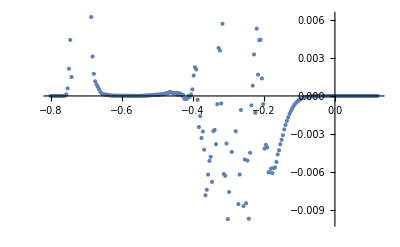

```mathematica
ListPlot[ynew]
```

```mathematica
funcform[gamma_,theta_]:=NIntegrate[surfen1[f]*i2 /.{l1->81, θ-> theta,γ->gamma},{f,0,1/(2π)}]
```

```mathematica
model[gamma_]:=Reap[For[i=1,i≤Length[data],i++,Sow[funcform[gamma,data[[i,1]]]]]][[2,1]];
```

```mathematica
NonlinearModelFit[ynew, model[gamma],{gamma} ,theta]
```

NIntegrate::inumr: The integrand -(7.58853 ⅇ^((-48.2994+«3»+«18» «1»)/((-1.+f) («1»))«1»729.664 «1»«1»«5») (1.02246-2.02246 f+1. f^2) √((1-f)/(1.02049-2.02049 f+1. f^2)))/(-1.02246+1. f) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,0.159155}}.

NIntegrate::inumr: The integrand -(7.58853 ⅇ^((-47.6101+«3»+«18» «1»)/((-1.+f) («1»))-«1») (1.02236-2.02236 f+1. f^2) √((1-f)/(1.02049-2.02049 f+1. f^2)))/(-1.02236+1. f) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,0.159155}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

$Aborted

## Fitting using numerical integration to find γ

```mathematica
Manipulate[Plot[i2*surfen[f] /. {f-> f2, l1-> 81},{θ,-0.8,.2}, PlotRange-> {0,0.01}],{f2,0.1,0.9}]
```

### γ unknown so do fitting

```mathematica
Inner[List,th,y,List];
```

```mathematica
γ=1
```

1

```mathematica
i2*surfen[f]/.{ l1->81}
```

-1/(-1.+1. f+0.0280367 θ)7.58853 ⅇ^((-14.6327+34.6116 f^3-102.902 θ-180.911 θ^2+f^2 (10.3977+158.261 θ)+f (-30.3767-55.3587 θ+180.911 θ^2))/((-1.+f) (-1.02049+1. f))-116.13 (Piecewise[{{2 f π, f≤1/(2 π)}, {1, f>1/(2 π)}, {0, True}}])) √((1-f)/(1.02049-2.02049 f+1. f^2)) (1.+1. f^2+f (-2.+0.0280367 θ)-0.0280367 θ)

```mathematica
func[θ_?NumericQ]:=i2*surfen[f]/.{ l1->81}

N[func[θ]]/.θ->-0.8
```

-(7.58853 2.71828^(-729.664 f+(-48.094+129.693 f-116.211 f^2+34.6116 f^3)/((-1.+f) (-1.02049+1. f))) (1.02243-2.02243 f+1. f^2) √((1.-1. f)/(1.02049-2.02049 f+1. f^2)))/(-1.02243+1. f)

```mathematica
NIntegrate[func[θ]/.θ->-0.7 , {f,0,1}]
```

5.43421×10^-16

```mathematica
NIntegrate[func[-0.8],{f,0,.1}]
```

NIntegrate::inumr: The integrand ConditionalExpression[398.253 ⅇ^(-116.13 Min[1,√f √Times[«2»]]) √((1-f) f) ((ⅇ^(14.3389 Power[«2»]+«14»+3.63212 Power[«2»] f Power[«2»] Power[«2»]) («1»))/(√(f (1.02049+Times[«2»]+Times[«2»])) (-1.+1. f+0.0280367 θ))+(ⅇ^(14.3389 Power[«2»]+«13»+«1»+«18» «4») («5»+«1»))/(√(f (1.02049+Times[«2»]+Times[«2»])) (-1.+1. f+0.0280367 θ))),0<f<1.] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,0.1}}.

NIntegrate[func[-0.8],{f,0,0.1}]

### With fixed surface tension, use the following to evaluate numerical integral

```mathematica
g=Reap[For [i=1,i<=Length[data], i++, Sow[ NIntegrate[i2*surfen[f]/.{θ-> data[[i,1]], l1->81},{f, 0, 1/(2π)}] +NIntegrate[i2*surfconst/.θ-> data[[i,1]],{f,1/(2π),1}] ]]][[2,1]];
```